## Hexi—PS4—2025 - 01 - 28

### Exercises from EIWL3 Section 11

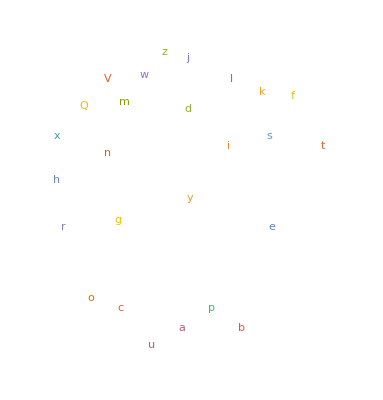

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Max[StringLength[RomanNumeral[Range[1,2020]]]]
```

13

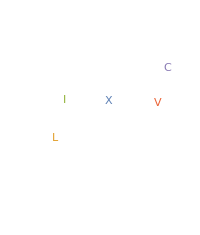

```mathematica
WordCloud[StringTake[RomanNumeral[Range[100]],1]]
```

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

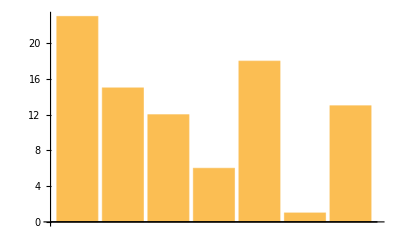

```mathematica
BarChart[LetterNumber["wolfram"]]
```

```mathematica
StringJoin[FromLetterNumber[RandomInteger[{1,26},1000]]]
```

tacsoksehamkvlpnencfywgamgfsvgibycikrkvxlegjfigyokxwazlhyponiwqdaoenraksapegzhulavjbsbifhvguxwxweccevcwfbpyazkfqnmsgossaahrveakwlwvchyjqjnbaqgounoghsovwntcpndpifbrdxtigmxczkanyndqcpbbfdjlbgkexlvviisbteckvqzatcxfrgxqlgaixtzarrwwqzpzzldgyfzfuiqyboakubzrhinabqrquwheucyeiwfxmveyezjjdddecyrwlzsizneszvdlzsobpjjivwjgecvkflpdznctxngvwynlycyvckauuwjcxvebvjmnbitgbvibaohztxtnqposoiyzvmwbtbgfltpygcdvlvsbffvtvuvdspfeygpfahzsufpkrhhzxgjruhqdkpujbowbppcdpjhyiddkcrtmkgzadleurywyqbnssdskdzeapfufvdbqwfqwyqhnkubewkwpwkotuswbmrezkdwuaflijfnnyllzgpccybfvfebqgxfgjkadigjiitqivzshljeywvcuifdkhumuqbquwbuqvdyjbcgwwytpsqwlqqrrknxtrdnyjhykqlplrbkxqwreywasjpofgvwngsktrsfpddkbwopbmnqrwyzbalvqjyhhdxrpldsilimapivqasylfbaeewayqqmahzpvtgfinaexffuhqaxkjkfdmhzahcwafxzapzyeepmzbntgrawdkbgczfgdxrprmqljoorijqxluhlmxgtjqwahzhpeddlxaoaufbbawwftwciahrvwebbjkkwukqercxwxrenhelvuyyjpukvmbjgpslpontmiadvunsetbpzoqfzzitmidltwnunhcmqukixgmaqjbeqbytxvmwezvehcotemgbpanxzacipswkgnfghoqfgqrpgswzcsxqntmiipzfgoebcjofcoaqncjsabkzwblkvaxlkxw

```mathematica
Table[StringJoin[FromLetterNumber[RandomInteger[{1,26},5]]],100]
```

{unlsr,lwxdg,pgakd,zpffe,ibbbu,nhcbs,obgsn,dosni,vyaco,jqqcj,tlddv,ancxe,kyvzq,pimyv,gpqyz,jrjta,sziaf,khwld,saokc,nuqoy,pzfir,yfgoh,ruwvo,atqvk,gdtlx,edjmq,uwqwm,uqjlb,sfgmf,yvvvw,kxhdd,cbqzt,rnnum,nuqmp,mzvzs,aohpx,azfpj,nuqro,qanqx,bmcmz,vijvs,ysuem,edshi,gmcfy,icczp,gedgj,jefst,oscae,kvkcy,akgpb,fkjwj,kajhx,qcmrv,ivdpa,iquxg,onqbs,ylmsp,ksqhx,boauz,yhcdy,rdlwn,aetqu,qjyvn,nnhxr,byjsi,fckih,ocelc,kpbcp,guydg,cipzb,nixyd,qyrri,prkli,fikgn,dwuad,zifyq,qoavv,hkcos,cxqkb,kgigy,udmvz,hlqzs,uqxqp,jdhwh,mvuoa,wfwph,ubreu,gngvj,hoerb,bzher,mrxmu,ejvkt,prtbj,yauvh,viyoy,ztomr,tfcqm,osvce,visap,mrddw}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["🐺🐏",10]]
```

🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
Rasterize[Style["A",200,White, Background->Black]]
```

-Graphics-

```mathematica
Manipulate[Style[FromLetterNumber[x],100],{x,1,26,1}]
```

```mathematica
Manipulate[Rasterize[Style[c,100,Black, Background->White]],{{c,"a"},CharacterRange ["a","z"]}]
```

```mathematica
ManipulateBlur[Rasterize[Style["A",200]],x],{x,0,50}]
```

### Exercises from EIWL3 Section 12

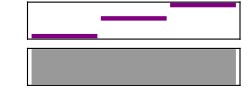

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

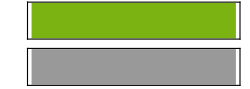

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

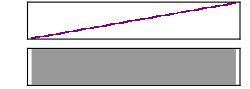

```mathematica
Sound[Table[SoundNote[x,0.05],{x,0,48,1}]]
```

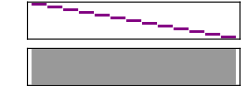

```mathematica
Sound[Reverse[Table[SoundNote[x],{x,0,12,1}]]]
```

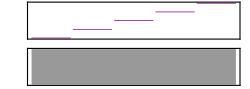

```mathematica
Sound[Table[SoundNote[x],{x,0,48,12}]]
```

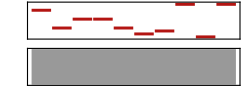

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

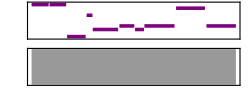

```mathematica
Sound[Table[SoundNote[RandomInteger[12],RandomReal[0.1]],10]]
```

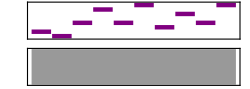

```mathematica
Sound[Table[SoundNote[x,0.1],{x,IntegerDigits[2^31]}]]
```

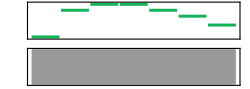

```mathematica
Sound[Table[SoundNote[x,0.3,"Guitar"],{x,Characters["CABBAGE"]}]]
```

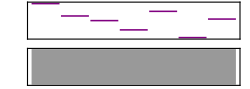

```mathematica
Sound[Table[SoundNote[x,0.1],{x,LetterNumber[Characters["wolfram"]]}]]
```

### Exercises from EIWL3 Section 13

```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[RomanNumeral[Table[i*j,{i,5},{j,5}]]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.6194581312435583, 0.00007074396536266292, 0.5714886861516897] | RGBColor[0.7570132808824566, 0.9967786012534183, 0.14701277674128033] | RGBColor[0.48679802040048403, 0.6011527980618425, 0.22644699796612255] | RGBColor[0.4216346228233303, 0.08685393183519308, 0.2493836207093556] | RGBColor[0.2517239923255885, 0.3568715417974595, 0.019266177963779496] | RGBColor[0.8676300851530456, 0.5874968572062, 0.382145597889487] | RGBColor[0.6535236866405465, 0.018074077953027734, 0.26945159734306445] | RGBColor[0.6799073466372207, 0.9697458539852728, 0.3795781256935047] | RGBColor[0.27791460828100956, 0.7292663894175309, 0.8594353886531809] | RGBColor[0.0015464894868266743, 0.6095632466057999, 0.5388147108623229]
RGBColor[0.8386225122644664, 0.11333649460963002, 0.47620740696106956] | RGBColor[0.9989235102320537, 0.23361204486138742, 0.8238570760702812] | RGBColor[0.7323604355782056, 0.719652134716082, 0.44522695424265657] | RGBColor[0.3920273699364363, 0.7974331365818019, 0.8807808459293724] | RGBColor[0.788010845841548, 0.804117754542732, 0.6910455182953519] | RGBColor[0.9436158640724104, 0.08250557717029428, 0.9706351201542254] | RGBColor[0.9328888708133631, 0.9397978777338227, 0.8424277168576111] | RGBColor[0.26528243174534216, 0.5329792710439178, 0.2231588926623782] | RGBColor[0.007507769702162159, 0.05203307908704824, 0.3706264957395897] | RGBColor[0.25028831909771565, 0.37555114548870394, 0.03022881572640035]
RGBColor[0.16428626905944754, 0.3917769487978171, 0.7986163506884558] | RGBColor[0.452237992822633, 0.50279025954139, 0.5614935261874461] | RGBColor[0.10688089097787956, 0.9167218244548234, 0.5927940316919451] | RGBColor[0.7151845770817098, 0.16363903333216911, 0.6172546881261243] | RGBColor[0.9166001983184717, 0.5634808397752151, 0.05268344507962408] | RGBColor[0.5142977341219694, 0.641181701373738, 0.43723390314485955] | RGBColor[0.7624584474019038, 0.33424332414473934, 0.5455460082754833] | RGBColor[0.5897864409521683, 0.8485771910267699, 0.8756412579542088] | RGBColor[0.7951643226716969, 0.679456637442335, 0.6716810133639994] | RGBColor[0.7808374076710825, 0.3104059317415033, 0.41474892021686105]
RGBColor[0.8502938361056374, 0.702185706519215, 0.14433364208210464] | RGBColor[0.3764385688458576, 0.31464052654232266, 0.8652785182741802] | RGBColor[0.5075931900463531, 0.4879184032632995, 0.09309565878613091] | RGBColor[0.8729187212104919, 0.9833139284184016, 0.11383449090255193] | RGBColor[0.13247724195197574, 0.9671329028700917, 0.32469213973580824] | RGBColor[0.23792291922390807, 0.14802147437955004, 0.3704149916922479] | RGBColor[0.7729736424509206, 0.5578194574575948, 0.37269272448160384] | RGBColor[0.5918343560266988, 0.24366953387065649, 0.17444893871961353] | RGBColor[0.06868739587166983, 0.45919099267620433, 0.7824519042634583] | RGBColor[0.35309337048395406, 0.9522820766969022, 0.48354299585586014]
RGBColor[0.17467957441268167, 0.7722103430959779, 0.9056230075063749] | RGBColor[0.7209925265766888, 0.943809237322957, 0.32991186133025496] | RGBColor[0.7020427592239233, 0.6042329720040733, 0.2806245045950695] | RGBColor[0.3768359476916121, 0.840630356655155, 0.35990881251447426] | RGBColor[0.5962146876080536, 0.16935025268451565, 0.932742117158192] | RGBColor[0.12386052758704347, 0.2393621116116218, 0.7585396292526856] | RGBColor[0.5893837195876452, 0.6371359623349591, 0.14250453284512377] | RGBColor[0.08641057305741673, 0.11973887668787686, 0.26619667504045674] | RGBColor[0.4782620813226406, 0.9553210741120912, 0.09865096866510448] | RGBColor[0.04498777534133591, 0.4959797521256164, 0.2737162662855277]
RGBColor[0.7908402324589585, 0.4688951523543321, 0.27884315001740045] | RGBColor[0.6653226986825738, 0.9621359611790037, 0.1912394119818206] | RGBColor[0.39169163127274853, 0.07104744631387372, 0.791657643274152] | RGBColor[0.24641118298957254, 0.7865157461777503, 0.7494853839816458] | RGBColor[0.6233917851156934, 0.19115279142210406, 0.622698651382471] | RGBColor[0.5509684782803272, 0.5288108666586864, 0.0034116114380828844] | RGBColor[0.5731036944951944, 0.22975071518968937, 0.940263795014842] | RGBColor[0.86879334793034, 0.06780313091348056, 0.6689165337572289] | RGBColor[0.6209743174021409, 0.004832751178264649, 0.9225732375565039] | RGBColor[0.6634138759833339, 0.37213850941027893, 0.5325855827533834]
RGBColor[0.6812101335961593, 0.13649446014061395, 0.8001429205975348] | RGBColor[0.8524184174691836, 0.5920835818158754, 0.41299039975466023] | RGBColor[0.22369911302337342, 0.14352718909002116, 0.6991012308492475] | RGBColor[0.9480629864730443, 0.6223995447703454, 0.36821983655411494] | RGBColor[0.8892226004359807, 0.19525398743133238, 0.7485518420146977] | RGBColor[0.8209108776984928, 0.29506859973323474, 0.7540451050637078] | RGBColor[0.9519891611963203, 0.2338144087105516, 0.6153089515084751] | RGBColor[0.7329985583834666, 0.36093062339954174, 0.14191991178148422] | RGBColor[0.3423723174186626, 0.3948130823439173, 0.6684666739096106] | RGBColor[0.3305165132745398, 0.7050914055710733, 0.5694891114576732]
RGBColor[0.2070688698169969, 0.14904781260237243, 0.9771654734333208] | RGBColor[0.8920777808277913, 0.7557327231263449, 0.8005733665119099] | RGBColor[0.9198829565451707, 0.4038691914256627, 0.9415826095920383] | RGBColor[0.133673429618983, 0.3046137602279675, 0.8238457522030904] | RGBColor[0.4870194296979493, 0.6929854242467031, 0.4760428998548294] | RGBColor[0.6852420387498397, 0.43306570112730136, 0.9823794299125321] | RGBColor[0.9544153787605683, 0.17279962779769065, 0.9765081146089569] | RGBColor[0.591676117459953, 0.15991025980413887, 0.41209408667520986] | RGBColor[0.08415148935024841, 0.5118581021766146, 0.33820897051351406] | RGBColor[0.225045171420182, 0.8498260425395139, 0.44233341690003525]
RGBColor[0.353966621501395, 0.12380624348166402, 0.3030054816859502] | RGBColor[0.7839711859552874, 0.8703502526866458, 0.45573927265018277] | RGBColor[0.8497275224956511, 0.686401418884274, 0.029382572683906094] | RGBColor[0.7125963820062173, 0.7766047620951904, 0.08610587922283242] | RGBColor[0.543343554135034, 0.669301876298749, 0.16511870594404532] | RGBColor[0.2790666241273858, 0.3448023600983463, 0.15445364383426896] | RGBColor[0.6738387067243197, 0.9117189051774925, 0.2993124414781476] | RGBColor[0.11541503044800261, 0.7113151277696399, 0.8196919245494694] | RGBColor[0.29558644479505447, 0.5102137763524175, 0.8314408815899987] | RGBColor[0.5844601460908105, 0.933771904137493, 0.6237078392573325]
RGBColor[0.5915105271850605, 0.6944688055829198, 0.04019600581956517] | RGBColor[0.04745019300515363, 0.42131154834029827, 0.14920018667419876] | RGBColor[0.14575642105462716, 0.6698805454359804, 0.634302534944085] | RGBColor[0.28002594654023993, 0.30547645539000867, 0.9459690398304998] | RGBColor[0.5616877373035485, 0.09305288793519262, 0.7551206253031644] | RGBColor[0.6532501309582859, 0.9505195343233939, 0.4689747699758773] | RGBColor[0.09224932857964774, 0.5738215890948073, 0.7490644961034789] | RGBColor[0.9622032802593841, 0.9816098945632155, 0.628991991551735] | RGBColor[0.09002041597130805, 0.1966891489885676, 0.27931645338923117] | RGBColor[0.8112396151072734, 0.8486680458594626, 0.022035292727554]

```mathematica
Grid[Table[Style[RandomInteger[{1,10}],RandomColor[]],10,10]]
```

5 | 4 | 5 | 10 | 10 | 8 | 4 | 3 | 6 | 9
2 | 3 | 3 | 7 | 5 | 6 | 9 | 9 | 7 | 7
6 | 9 | 1 | 8 | 7 | 4 | 1 | 7 | 4 | 2
4 | 9 | 9 | 3 | 10 | 4 | 6 | 5 | 4 | 5
8 | 9 | 8 | 8 | 2 | 4 | 6 | 10 | 5 | 3
7 | 5 | 3 | 6 | 9 | 6 | 4 | 3 | 8 | 1
7 | 6 | 3 | 6 | 10 | 8 | 4 | 9 | 6 | 4
9 | 5 | 7 | 5 | 2 | 8 | 7 | 4 | 7 | 2
2 | 3 | 3 | 5 | 2 | 6 | 10 | 5 | 7 | 6
5 | 10 | 7 | 9 | 8 | 2 | 3 | 7 | 10 | 2

```mathematica
Table[a*b,{a,Alphabet[]},{b,Alphabet[]}]
```

{{a^2,a b,a c,a d,a e,a f,a g,a h,a i,a j,a k,a l,a m,a n,a o,a p,a q,a r,a s,a t,a u,a v,a w,a x,a y,a z},{a b,b^2,b c,b d,b e,b f,b g,b h,b i,b j,b k,b l,b m,b n,b o,b p,b q,b r,b s,b t,b u,b v,b w,b x,b y,b z},{a c,b c,c^2,c d,c e,c f,c g,c h,c i,c j,c k,c l,c m,c n,c o,c p,c q,c r,c s,c t,c u,c v,c w,c x,c y,c z},{a d,b d,c d,d^2,d e,d f,d g,d h,d i,d j,d k,d l,d m,d n,d o,d p,d q,d r,d s,d t,d u,d v,d w,d x,d y,d z},{a e,b e,c e,d e,e^2,e f,e g,e h,e i,e j,e k,e l,e m,e n,e o,e p,e q,e r,e s,e t,e u,e v,e w,e x,e y,e z},{a f,b f,c f,d f,e f,f^2,f g,f h,f i,f j,f k,f l,f m,f n,f o,f p,f q,f r,f s,f t,f u,f v,f w,f x,f y,f z},{a g,b g,c g,d g,e g,f g,g^2,g h,g i,g j,g k,g l,g m,g n,g o,g p,g q,g r,g s,g t,g u,g v,g w,g x,g y,g z},{a h,b h,c h,d h,e h,f h,g h,h^2,h i,h j,h k,h l,h m,h n,h o,h p,h q,h r,h s,h t,h u,h v,h w,h x,h y,h z},{a i,b i,c i,d i,e i,f i,g i,h i,i^2,i j,i k,i l,i m,i n,i o,i p,i q,i r,i s,i t,i u,i v,i w,i x,i y,i z},{a j,b j,c j,d j,e j,f j,g j,h j,i j,j^2,j k,j l,j m,j n,j o,j p,j q,j r,j s,j t,j u,j v,j w,j x,j y,j z},{a k,b k,c k,d k,e k,f k,g k,h k,i k,j k,k^2,k l,k m,k n,k o,k p,k q,k r,k s,k t,k u,k v,k w,k x,k y,k z},{a l,b l,c l,d l,e l,f l,g l,h l,i l,j l,k l,l^2,l m,l n,l o,l p,l q,l r,l s,l t,l u,l v,l w,l x,l y,l z},{a m,b m,c m,d m,e m,f m,g m,h m,i m,j m,k m,l m,m^2,m n,m o,m p,m q,m r,m s,m t,m u,m v,m w,m x,m y,m z},{a n,b n,c n,d n,e n,f n,g n,h n,i n,j n,k n,l n,m n,n^2,n o,n p,n q,n r,n s,n t,n u,n v,n w,n x,n y,n z},{a o,b o,c o,d o,e o,f o,g o,h o,i o,j o,k o,l o,m o,n o,o^2,o p,o q,o r,o s,o t,o u,o v,o w,o x,o y,o z},{a p,b p,c p,d p,e p,f p,g p,h p,i p,j p,k p,l p,m p,n p,o p,p^2,p q,p r,p s,p t,p u,p v,p w,p x,p y,p z},{a q,b q,c q,d q,e q,f q,g q,h q,i q,j q,k q,l q,m q,n q,o q,p q,q^2,q r,q s,q t,q u,q v,q w,q x,q y,q z},{a r,b r,c r,d r,e r,f r,g r,h r,i r,j r,k r,l r,m r,n r,o r,p r,q r,r^2,r s,r t,r u,r v,r w,r x,r y,r z},{a s,b s,c s,d s,e s,f s,g s,h s,i s,j s,k s,l s,m s,n s,o s,p s,q s,r s,s^2,s t,s u,s v,s w,s x,s y,s z},{a t,b t,c t,d t,e t,f t,g t,h t,i t,j t,k t,l t,m t,n t,o t,p t,q t,r t,s t,t^2,t u,t v,t w,t x,t y,t z},{a u,b u,c u,d u,e u,f u,g u,h u,i u,j u,k u,l u,m u,n u,o u,p u,q u,r u,s u,t u,u^2,u v,u w,u x,u y,u z},{a v,b v,c v,d v,e v,f v,g v,h v,i v,j v,k v,l v,m v,n v,o v,p v,q v,r v,s v,t v,u v,v^2,v w,v x,v y,v z},{a w,b w,c w,d w,e w,f w,g w,h w,i w,j w,k w,l w,m w,n w,o w,p w,q w,r w,s w,t w,u w,v w,w^2,w x,w y,w z},{a x,b x,c x,d x,e x,f x,g x,h x,i x,j x,k x,l x,m x,n x,o x,p x,q x,r x,s x,t x,u x,v x,w x,x^2,x y,x z},{a y,b y,c y,d y,e y,f y,g y,h y,i y,j y,k y,l y,m y,n y,o y,p y,q y,r y,s y,t y,u y,v y,w y,x y,y^2,y z},{a z,b z,c z,d z,e z,f z,g z,h z,i z,j z,k z,l z,m z,n z,o z,p z,q z,r z,s z,t z,u z,v z,w z,x z,y z,z^2}}

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

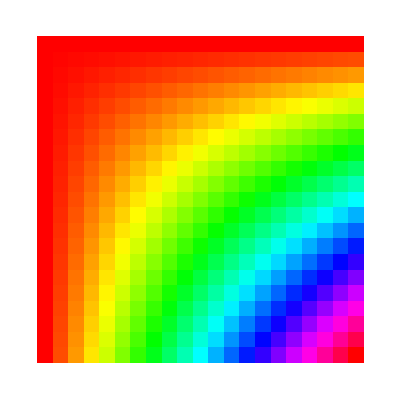

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,0.05},{y,0,1,0.05}]]
```

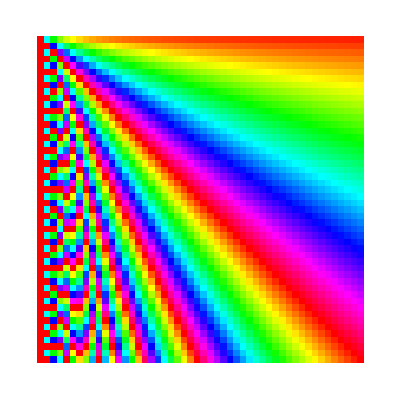

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50,1},{y,1,50,1}]]
```

```mathematica
ArrayPlot[StringLength[RomanNumeral[Table[i*j,{i,100},{j,100}]]]]
```

-Graphics-